```mathematica
ClearAll[c,G,MSun,rhoRadBBN];

c=29979245800;                   (*velocidad de la luz:cm/s*)
G=66743/10^12;                   (*constante gravitacional:cm^3/(g s^2)*)
MSun=198847*10^28;               (*masa solar:g*)

rhoRadBBN=7331305019814086*10^11;
(*densidad de energía de radiación en BBN:erg/cm^3*)
```

```mathematica
ti=37/50;                       (*coordenada temporal de BBN:0.74 s*)
ai=83/500000000000;             (*factor de escala en BBN:1.66*10^-10*)
Hti=67/100;                     (*parámetro de Hubble en BBN:0.67 s^-1*)
```

```mathematica
ρ0[ξ_]:= ξ*rhoRadBBN
```

```mathematica
Cxi[ξ_]:= (4π G)/(3c^2)*ρ0[ξ]
```

```mathematica
N[-3/4]
```

-0.75

```mathematica
ClearAll[sol];
```

```mathematica
tMin=-5;
(* n = -0.5 luego 
(Y[t])^((n-1)/2) ----> Y^-1
*)
```

```mathematica
ClearAll[sol,tBounce]
```

```mathematica
sol[ξ_]:=sol[ξ]=Quiet@NDSolve[{Y'[t]==v[t],v'[t]==2*Cxi[ξ]*(Y[t])^(-3/4),Y[ti]==1,v[ti]==2*Hti,WhenEvent[v[t]==0,"StopIntegration"]},{Y,v},{t,-1,ti},WorkingPrecision->40,AccuracyGoal->20,PrecisionGoal->20,Method->"StiffnessSwitching",MaxSteps->Infinity];
```

```mathematica
tBounce[ξ_]:=tBounce[ξ]=(Y/. sol[ξ][[1]])["Domain"][[1,1]];
```

```mathematica
tB= tBounce[1/10]
```

-0.02226543291352760601285068529612728748794

```mathematica
Yfunc[ξ_,t_]:=Y[t]/. sol[ξ][[1]];
vFunc[ξ_,t_]:=v[t]/. sol[ξ][[1]];
```

```mathematica
apos[ξ_,t_]:=ai*Sqrt[Yfunc[ξ,Abs[t]+tBounce[ξ]]];
```

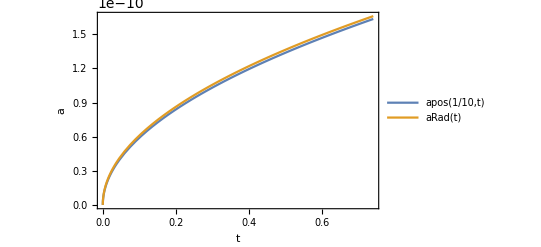

```mathematica
ar := ai/ti^(1/2)
aRad[t_]:= ar*t^(1/2)
Plot[{apos[1/10, t],aRad[t]},{t,0,ti},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0, PlotLegends->"Expressions"]
```

```mathematica
ρbh[ξ_,t_]:= ρ0[ξ]*(ai/apos[ξ, t])^4
```

```mathematica
ρbh[1/10,0]
```

3.×10^104

```mathematica
ρbh[1/10, 10^(-4)]
```

5.0169652538263248302350337643135012×10^33

```mathematica
DotA[ξ_,t_]:=Sign[t]*(ai^2*vFunc[ξ,Abs[t]+tBounce[ξ]])/(2*apos[ξ,t]);
```

```mathematica
DotA[1/10, 0]
```

0

```mathematica
ρrad[ξ_, t_]:= (3c^2)/(8π G)(DotA[ξ, t]/apos[ξ, t])^2 -ρbh[ξ, t]
```

```mathematica
ρrad[1/10, 10^(-4)]
```

3.53785559146124489758531590288655267×10^34

```mathematica
ρrad[1/10, 0]
```

-3.×10^104

```mathematica
HubbleParameter[ξ_, t_]:= √((8π G)/(3c^2)(ρrad[ξ, t]+ρbh[ξ, t]))
```

```mathematica
HubbleParameter[1/10, 0]
```

0``-38.19943737165658

```mathematica
HubbleParameter[1/10, 10^(-4)]
```

5013.11963829225017594259425092439032

```mathematica
5289.5069196841113186285097189208109531727050978632872936576626`36.94221135751255/5000
```

1.05790138393682226372570194378416219

```mathematica
MHubble[ξ_, t_]:= (4π c)/3*(ρrad[ξ, t]+ρbh[ξ, t])/(HubbleParameter[ξ, t])^3
```

```mathematica
γ := 0.2
Minic[ξ_, t_] := γ*MHubble[ξ, t]
```

```mathematica
Minic[1/10, 10^(-4)]
```

8.05283×10^33

```mathematica
Minic[1/10,10^(-4)]/MSun
```

4.04976

```mathematica
β = ρbh[1/10, 10^(-4)]/(ρrad[1/10, 10^(-4)]+ρbh[1/10, 10^(-4)])
```

0.124196076909291253456228267106671173

```mathematica
xiCompareValues=10^-Range[10];
```

```mathematica
tForm=10^(-4);
```

```mathematica
tablaDatos=N[Table[{xi,HubbleParameter[xi,tForm],MHubble[xi,tForm],Minic[xi,tForm],Minic[xi,tForm]/MSun, ρbh[xi,tForm]/(ρrad[xi,tForm]+ρbh[xi,tForm])},{xi,xiCompareValues}],18];
```

```mathematica
datos= Grid[Prepend[tablaDatos,{"ξ","H","\!\(\*SubscriptBox[\(M\), \(H\)]\)","\!\(\*SubscriptBox[\(M\), \(inic\)]\)","\!\(\*SubscriptBox[\(M\), \(inic\)]\)[MSun]", "β"}],Frame->All,Background->{None,{LightGray,None}},Alignment->Left]
```

ξ | H | M_H | M_inic | M_inic[MSun] | β
0.1 | 5013.11963829225018 | 4.02641300631840493×10^34 | 8.05283×10^33 | 4.04976 | 0.124196076909291253
0.01 | 5001.11144927476719 | 4.03608084294486819×10^34 | 8.07216×10^33 | 4.05948 | 0.0103482024215271328
0.001 | 5000.10950211523256 | 4.03688961317970605×10^34 | 8.07378×10^33 | 4.0603 | 0.00101789485496963195
0.0001 | 5000.01094257579309 | 4.03696918780176437×10^34 | 8.07394×10^33 | 4.06038 | 0.000101623317882940227
0.00001 | 5000.00109412081978 | 4.03697713938187931×10^34 | 8.07395×10^33 | 4.06039 | 0.0000101606731665084159
1.×10^-6 | 5000.00010932233277 | 4.03697793450365772×10^34 | 8.07396×10^33 | 4.06039 | 1.01605073348604114×10^-6
1.×10^-7 | 5000.00001093236435 | 4.03697801394328384×10^34 | 8.07396×10^33 | 4.06039 | 1.0160490751741778×10^-7
1.×10^-8 | 5000.00000109343138 | 4.03697802188719506×10^34 | 8.07396×10^33 | 4.06039 | 1.01604890934328642×10^-8
1.×10^-9 | 5000.00000010958495 | 4.03697802268154834×10^34 | 8.07396×10^33 | 4.06039 | 1.01604889276019009×10^-9
1.×10^-10 | 5000.00000001093179 | 4.03697802276120047×10^34 | 8.07396×10^33 | 4.06039 | 1.01604889110195451×10^-10

```mathematica
formationHeaders = {"ξ", "H(t_form)","MHubble","Minic [g]", "Minic [Msun]", "β"};
```

```mathematica
csvPath=FileNameJoin[{NotebookDirectory[],"tabla_formacion_nm05.csv"}];
```

```mathematica
Export[csvPath,Prepend[tablaDatos,formationHeaders],"CSV"]
```

/home/iara/doctorado/tres incognitas/tabla_formacion_nm05.csv

```mathematica
ClearAll[pdfPath];

(*La tabla visual se exporta como PDF en la misma carpeta en la que se encuentra guardado el notebook.*)

pdfPath=FileNameJoin[{NotebookDirectory[],"tabla_formacion_nm05.pdf"}];

Export[pdfPath,datos,"PDF"]
```

/home/iara/doctorado/tres incognitas/tabla_formacion_nm05.pdf